```mathematica
f[N_]:=1+Sum[Subscript[f,n] r^n,{n,1,N}]
Collect[Series[-2/r+2/r Exp[-α r]f[30],{r,0,3}],r,FullSimplify]
```

2 (-α+f_1)+r (α^2-2 α f_1+2 f_2)+r^2 (-α^3/3+α^2 f_1-2 α f_2+2 f_3)+r^3 (α^4/12-(α^3 f_1)/3+α^2 f_2-2 α f_3+2 f_4)

```mathematica
f[N_]:=1+Sum[Subscript[f,n] r^n,{n,1,N}]
Collect[Series[-2/r+2/r Exp[-α r]f[30],{r,0,3}]/.{Subscript[f, 1]->-U0/2+α,Subscript[f, 2]->-(α^2-2 α (-U0/2+α))/2,Subscript[f, 3]->-(-α^3/3+α^2 (-U0/2+α)-α (-α^2+2 α (-U0/2+α)))/2},r,FullSimplify]
```

-U0+r^3 (1/12 (2 U0-α) α^3+2 f_4)

```mathematica
f[N_]:=1+Sum[Subscript[f,n] r^n,{n,1,N}]
Collect[Series[-2/r+2/r Exp[-α r]f[30],{r,0,5}]/.{Subscript[f, 1]->1/2(2α-1),Subscript[f, 2]->1/2(α(2α-2))/2,Subscript[f, 3]->1/2 (α^2(2α-3))/6,Subscript[f, 4]->1/2 (α^3(2α-4))/24},r,FullSimplify]
```

-1+r^4 (1/120 (5-2 α) α^4+2 f_5)+r^5 (1/360 α^5 (-12+5 α)-2 α f_5+2 f_6)

```mathematica
Clear[f,g];
f[𝒩_]:=1/(2α)Sum[(α r)^n/(n!)(2α-n),{n,0,𝒩}]
g[𝒩_]:=-2/r+2/r Exp[-α r]f[𝒩]
Table[Collect[Series[g[𝒩],{r,0,𝒩+1}]//Normal,r,FullSimplify],{𝒩,1,5}]
```

{-1-r (-1+α) α+1/6 r^2 α^2 (-3+4 α),-1+1/6 r^2 (3-2 α) α^2+1/12 r^3 α^3 (-4+3 α),-1-1/12 r^3 (-2+α) α^3+1/120 r^4 α^4 (-15+8 α),-1+1/120 r^4 (5-2 α) α^4+1/360 r^5 α^5 (-12+5 α),-1-1/360 r^5 (-3+α) α^5+(r^6 α^6 (-35+12 α))/5040}

```mathematica
Clear[Ci];
Ci[n_]:=(α r)^n/(n!)(2α-n)
Ci[n]/Ci[n-1]//FullSimplify
Limit[(Ci[n]/Ci[n-1])/.{α->n/2+δ,r->2}//FullSimplify,n->∞]
```

(r (n-2 α) α)/(n (-1+n-2 α))

(2 δ)/(1+2 δ)

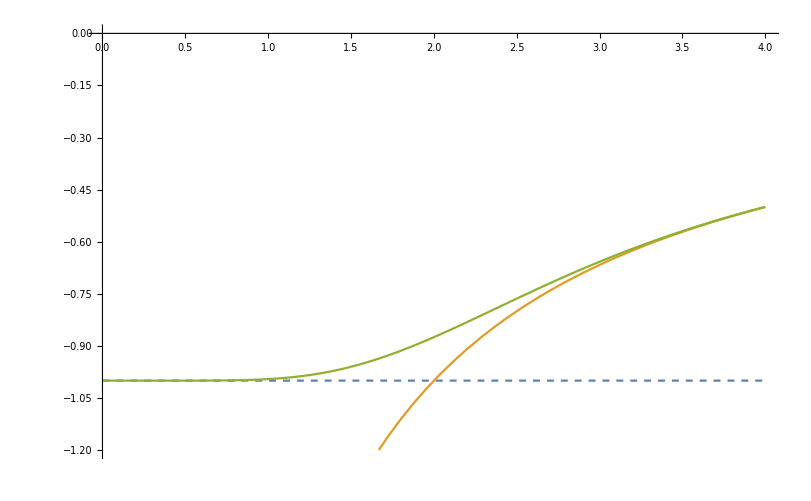

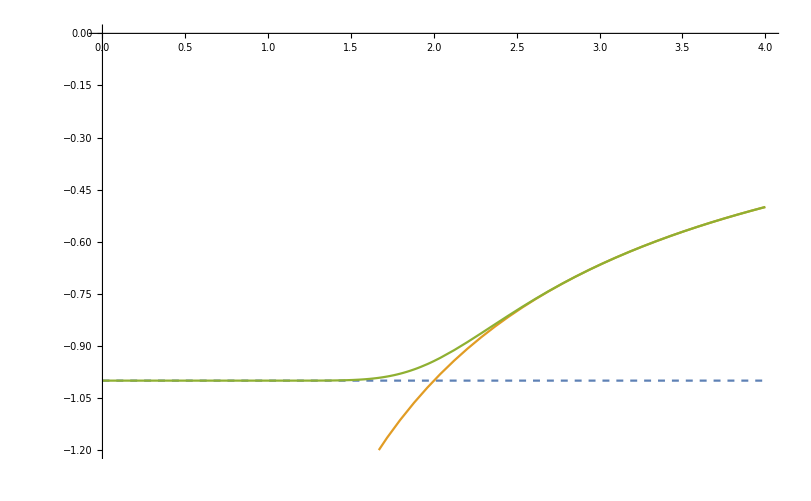

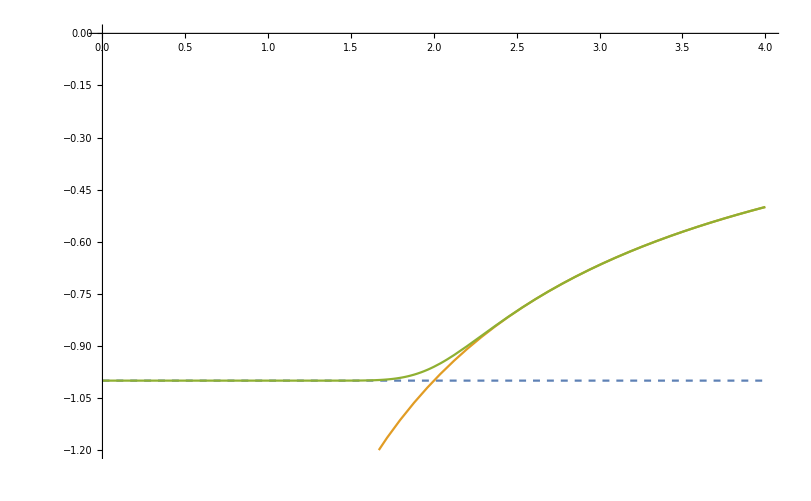

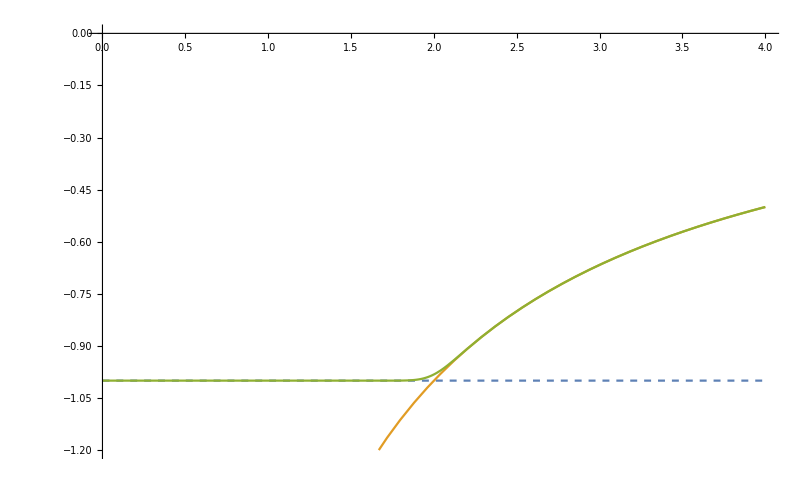

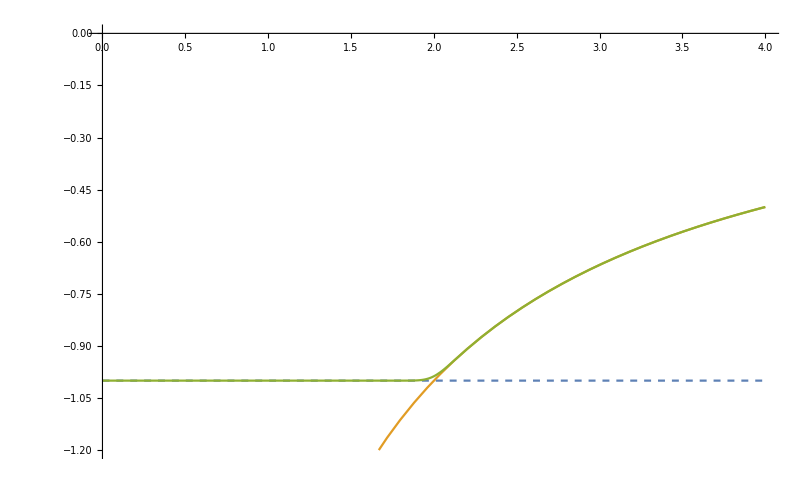

```mathematica
Clear[f,g];
f[𝒩_,α_]:=1/(2α)Sum[(α r)^n/(n!)(2α-n),{n,0,𝒩}]
g[𝒩_,α_]:=-2/r+2/r Exp[-α r]f[𝒩,α]
plt[xp_]:=Plot[{Style[-1,Dashed],-2/r,xp},{r,0,4},PlotRange->{-1.2,0},WorkingPrecision->240,PerformanceGoal->"Quality"]
Off[General::munfl];
Do[
gexp=g[𝒩,𝒩/2];
plt[gexp]//Print;
,{𝒩,{10,50,100,500,1000}}
]
On[General::munfl];
```

```mathematica
Clear[f];
f[𝒩_]:=1+Sum[Subscript[f,n] r^n,{n,1,𝒩}]
Collect[Series[-2/r+2/r Exp[-(ℬ r)^2]f[60],{r,0,10}]/.{Subscript[f, 1]->-U0/2,Subscript[f, 3]->-(U0 ℬ^2)/2,Subscript[f, 5]->-(U0 ℬ^4)/4,Subscript[f, 7]->-(U0 ℬ^6)/12,Subscript[f, 2]->ℬ^2,Subscript[f, 4]->ℬ^4/2,Subscript[f, 6]->ℬ^6/6,Subscript[f, 8]->ℬ^8/24},r,FullSimplify]
```

-U0+2 r^8 ((U0 ℬ^8)/48+f_9)+r^9 (-ℬ^10/60+2 f_10)+2 r^10 (-(U0 ℬ^10)/60-ℬ^2 f_9+f_11)

```mathematica
Clear[f,g];
f[𝒩_]:=(1-r/2)(Sum[(ℬ r)^(2n)/(n!),{n,0,𝒩-1}])+(ℬ r)^(2𝒩)/(𝒩!)
g[𝒩_]:=-2/r+2/r Exp[-(ℬ r)^2]f[𝒩]
Table[Collect[Series[g[𝒩],{r,0,2𝒩+1}],FullSimplify],{𝒩,1,5}]
```

{-1+ℬ^2 r^2-ℬ^4 r^3+O[r]^4,-1+(ℬ^4 r^4)/2-(ℬ^6 r^5)/3+O[r]^6,-1+(ℬ^6 r^6)/6-(ℬ^8 r^7)/12+O[r]^8,-1+(ℬ^8 r^8)/24-(ℬ^10 r^9)/60+O[r]^10,-1+(ℬ^10 r^10)/120-(ℬ^12 r^11)/360+O[r]^12}

```mathematica
Clear[Ci];
Ci[𝒩_]:=(ℬ r)^(2𝒩)/(𝒩!)
Ci[n]/Ci[n-1]//FullSimplify
Limit[(Ci[n]/Ci[n-1])/.{ℬ->(√n)/2+δ,r->2}//FullSimplify,n->∞]
```

(r^2 ℬ^2)/n

1

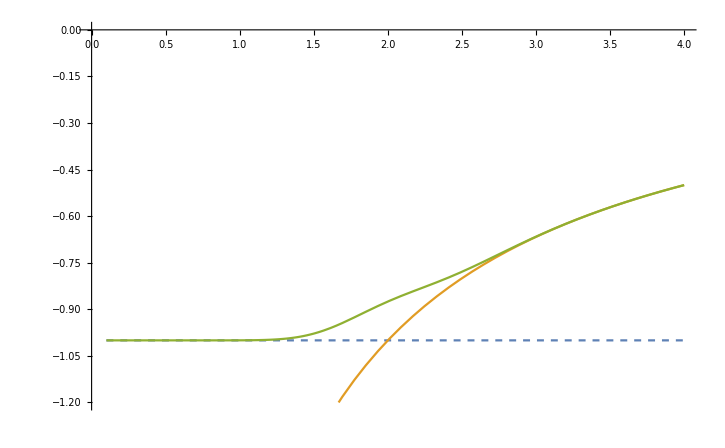

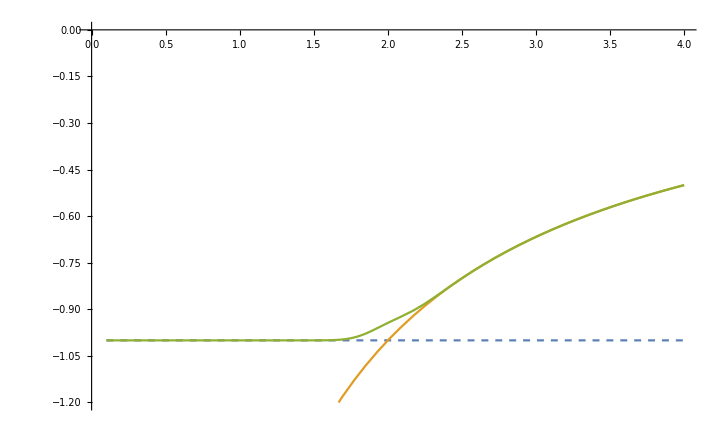

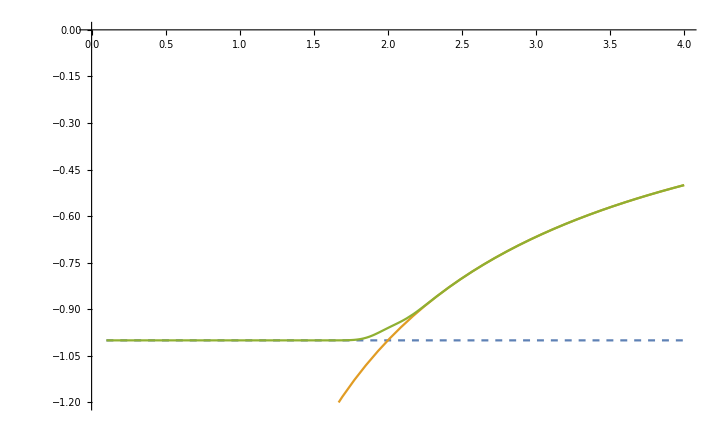

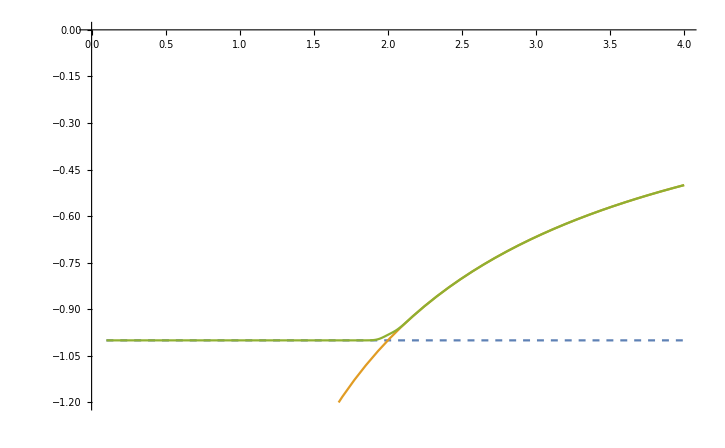

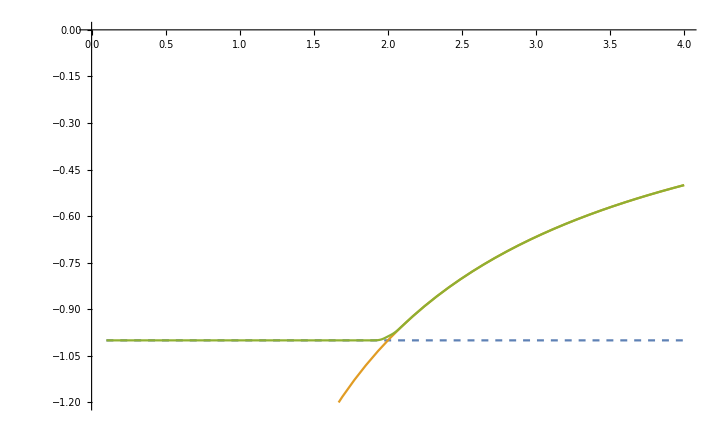

```mathematica
Clear[f,g,prec]
prec=240;
f[𝒩_,ℬ_]:=(1-r/2)(Sum[(ℬ r)^(2n)/(n!),{n,0,𝒩-1}])+(ℬ r)^(2𝒩)/(𝒩!);
g[N_,ℬ_]:=-2/r+2/r Exp[-(ℬ r)^2]f[N,ℬ];
plt[xp_]:=Plot[{Style[-1,Dashed],-2/r,xp},{r,0.1,4},PlotRange->{-1.2,0},WorkingPrecision->prec,PerformanceGoal->"Quality"]
Off[General::munfl];
Do[
gexp=SetPrecision[g[𝒩,(√𝒩)/2],prec];
plt[gexp]//Print;
,{𝒩,{10,50,100,500,1000}}
]
On[General::munfl];
```